```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Initial Params*)
startexec = DateObject[];
nsources = 2*10^6;
fluxmin = 5*10^-5;
fluxmax = 5*10^1;
fluxerr = 10^-1;
dmin = 7*10^-4;
dmax = 3*10^3;
detThreshold = 5.0;
extraThreshold = 3.0;
file = "output";
transientType = "tophat";
```

```mathematica
(*Simulate Observations*)
(*start, dur, sensitivity. in Days and Jy.Choice of Gaussian and its characteristics were arbitrary.*)
obs =Table[{UnixTime[]/(60*60*24)+i*7 //N,0.009,RandomVariate[NormalDistribution[0.0000317,0.0000046]]*detThreshold},{i,1,46}];
```

```mathematica
(*Simulate Sources*)
session = StartExternalSession["Python"]
ExternalEvaluate[session,"
import numpy as np
import random"]
ExternalEvaluate[session,"bursts = np.zeros(("<>ToString[nsources//CForm]<>", 3), dtype=np.float32)"]
ExternalEvaluate[session,"bursts[:,1] = np.absolute(np.power(10, np.random.uniform(np.log10("<>ToString[dmin//CForm]<>"), np.log10("<>ToString[dmax//CForm]<>"), "<>ToString[nsources//CForm]<>")))"]
ExternalEvaluate[session,"bursts[:,2] = np.absolute(np.power(10, np.random.uniform(np.log10("<>ToString[fluxmin//CForm]<>"),np.log10("<>ToString[fluxmax//CForm]<>"),"<>ToString[nsources//CForm]<>")))"]
ExternalEvaluate[session,"bursts[:,0] = np.random.uniform("<>ToString[obs[[1,1]]//CForm]<>"- bursts[:,1], "<>ToString[obs[[Length[obs],1]] + obs[[Length[obs],2]]//CForm]<>", "<>ToString[nsources//CForm]<>")"]
```

ExternalSessionObject[…]

```mathematica
(*Detect Simulated Sources*)
ExternalEvaluate[session,"detection = np.array([],dtype=np.uint32)"];
ExternalEvaluate[session,"extra_detection = np.array([],dtype=np.uint32)"];
```

```mathematica
If[transientType == "fred",For[i=1,i<(Length[obs]+1),i++, ExternalEvaluate[session,"start_obs, duration,sensitivity = "<>ToString[obs[[i]]]<>"
extra_sensitivity = sensitivity * ("<>ToString[detThreshold//CForm]<>" + "<>ToString[extraThreshold//CForm]<>") / "<>ToString[detThreshold//CForm]<>"
end_obs = start_obs + duration
candidate = np.where(sources[:,0] < end_obs)[0]
F0_o = bursts[candidate][:,2]
error = np.sqrt((abs(random.gauss(F0_o * "<>ToString[fluxerr//CForm]<>", 0.05 * F0_o * "<>ToString[fluxerr//CForm]<>")))**2 + (sensitivity/"<>ToString[detThreshold//CForm]<>")**2)#
F0 = random.gauss(F0_o, error)
tau = bursts[candidate][:,1]
t_burst = bursts[candidate][:,0]
tstart = np.maximum(t_burst, start_obs) - t_burst
tend = end_obs - t_burst
flux_int = np.multiply(F0, np.multiply(tau, np.divide(np.exp(-np.divide(tstart,tau)) - np.exp(-np.divide(tend,tau)), (end_obs-start_obs))))
candidates = candidate[(flux_int > sensitivity)]
extra_candidates = np.array(candidate[flux_int > extra_sensitivity])
detection = np.append(detection, candidates)
extra_detection = np.append(extra_detection, extra_candidates)"];];
ExternalEvaluate[session,"
def unique_count(a):
    unique, inverse = np.unique(a, return_inverse=True)
    count = np.zeros(len(unique), np.int)
    np.add.at(count, inverse, 1)
    return [unique, count]

dets = unique_count(detection)
detections = dets[0][np.where(dets[1] < "<>ToString[Length[obs]//CForm]<>")[0]]
detections = detections[(np.in1d(detections, extra_detection))]
detected_bursts = bursts[detections]
flux_ints = np.geomspace("<>ToString[fluxmin//CForm]<>", "<>ToString[fluxmax//CForm]<>", num=(np.log10("<>ToString[fluxmax//CForm]<>")-np.log10("<>ToString[fluxmin//CForm]<>"))/0.05, endpoint=True)
dur_ints = np.geomspace("<>ToString[dmin//CForm]<>", "<>ToString[dmax//CForm]<>", num=(np.log10("<>ToString[dmax//CForm]<>")-np.log10("<>ToString[dmin//CForm]<>"))/0.05, endpoint=True)

fluxes = np.array([],dtype=np.float32)
durations = np.array([],dtype=np.float32)

stats = np.zeros(((len(flux_ints)-1)*(len(dur_ints)-1), 5), dtype=np.float32)
    
alls = np.array([],dtype=np.uint32)
dets = np.array([],dtype=np.uint32)
    
doit_f = True
for i in range(len(dur_ints) - 1):
    all_dur = np.array([],dtype=np.uint32)
    det_dur = np.array([],dtype=np.uint32)

    all_dur = np.append(all_dur, np.where((bursts[:,1] >= dur_ints[i]) & (bursts[:,1] < dur_ints[i+1]))[0])
    det_dur = np.append(det_dur, np.where((detected_bursts[:,1] >= dur_ints[i]) & (detected_bursts[:,1] < dur_ints[i+1]))[0])
    durations = np.append(durations, dur_ints[i] + dur_ints[i+1]/2.)

    for m in range(len(flux_ints) - 1):
        dets = np.append(dets, float(len(np.where((detected_bursts[det_dur,2] >= flux_ints[m]) & (detected_bursts[det_dur,2]< flux_ints[m+1]))[0])))
        alls = np.append(alls, float(len(np.where((bursts[all_dur,2] >= flux_ints[m]) & (bursts[all_dur,2] < flux_ints[m+1]))[0])))

        if doit_f == True:
            fluxes = np.append(fluxes,  (flux_ints[m] + flux_ints[m+1])/2.)

    doit_f = False

probabilities = np.zeros(len(alls),dtype=np.float32)
toprint_alls = alls[np.where((alls[:] != 0.))]
toprint_dets = dets[np.where((alls[:] != 0.))]

probabilities[np.where((alls[:] != 0.))] = dets[np.where((alls[:] != 0.))] / alls[np.where((alls[:] != 0.))]
    
stats[:,0] = np.repeat(durations, len(fluxes))
stats[:,1] = np.tile(fluxes, len(durations))
stats[:,2] = probabilities
stats[:,3] = dets
stats[:,4] = alls
stats.astype('float32').tofile('stats.dat')"]
,Print["Not fred"]]
```

Not fred

```mathematica
(*If tophat*)
If[transientType == "tophat",For[i=1, i<(Length[obs]+1),i++,ExternalEvaluate[session,"start_obs, duration,sensitivity = "<>ToString[obs[[i,1]]//CForm]<>","<>ToString[obs[[i,2]]//CForm]<>","<>ToString[obs[[i,3]]//CForm]<>"
extra_sensitivity = sensitivity * ("<>ToString[detThreshold//CForm]<>" + "<>ToString[extraThreshold//CForm]<>") / "<>ToString[detThreshold//CForm]<>"
end_obs = start_obs + duration
candidate = np.where((bursts[:,0] + bursts[:,1] > start_obs) & (bursts[:,0] < end_obs))[0]
F0_o = bursts[candidate][:,2]
error = np.sqrt((abs(random.gauss(F0_o * "<>ToString[fluxerr//CForm]<>", 0.05 * F0_o * "<>ToString[fluxerr//CForm]<>")))**2 + (sensitivity/"<>ToString[detThreshold//CForm]<>")**2)#
F0 = random.gauss(F0_o, error)
tau = bursts[candidate][:,1]
t_burst = bursts[candidate][:,0]
tstart = np.maximum(t_burst, start_obs) - t_burst
tend = np.minimum(t_burst + tau, end_obs) - t_burst
flux_int = np.multiply(F0, np.divide((tend - tstart), (end_obs-start_obs)))
candidates = candidate[(flux_int > sensitivity)]
extra_candidates = np.array(candidate[flux_int > extra_sensitivity])
detection = np.append(detection, candidates)
extra_detection = np.append(extra_detection, extra_candidates)"]];
ExternalEvaluate[session,"
def unique_count(a):
    unique, inverse = np.unique(a, return_inverse=True)
    count = np.zeros(len(unique), np.int)
    np.add.at(count, inverse, 1)
    return [unique, count]

dets = unique_count(detection)
detections = dets[0][np.where(dets[1] < "<>ToString[Length[obs]//CForm]<>")[0]]
detections = detections[(np.in1d(detections, extra_detection))]
detected_bursts = bursts[detections]
flux_ints = np.geomspace("<>ToString[fluxmin//CForm]<>", "<>ToString[fluxmax//CForm]<>", num=(np.log10("<>ToString[fluxmax//CForm]<>")-np.log10("<>ToString[fluxmin//CForm]<>"))/0.05, endpoint=True)
dur_ints = np.geomspace("<>ToString[dmin//CForm]<>", "<>ToString[dmax//CForm]<>", num=(np.log10("<>ToString[dmax//CForm]<>")-np.log10("<>ToString[dmin//CForm]<>"))/0.05, endpoint=True)

fluxes = np.array([],dtype=np.float32)
durations = np.array([],dtype=np.float32)
stats = np.zeros(((len(flux_ints)-1)*(len(dur_ints)-1), 5), dtype=np.float32)
    
alls = np.array([],dtype=np.uint32)
detected_to_calculate = np.array([],dtype=np.uint32)
    
doit_f = True
for i in range(len(dur_ints) - 1):
    all_dur = np.array([],dtype=np.uint32)
    det_dur = np.array([],dtype=np.uint32)

    all_dur = np.append(all_dur, np.where((bursts[:,1] >= dur_ints[i]) & (bursts[:,1] < dur_ints[i+1]))[0])
    det_dur = np.append(det_dur, np.where((detected_bursts[:,1] >= dur_ints[i]) & (detected_bursts[:,1] < dur_ints[i+1]))[0])
    durations = np.append(durations, dur_ints[i] + dur_ints[i+1]/2.)

    for m in range(len(flux_ints) - 1):
        detected_to_calculate = np.append(detected_to_calculate, float(len(np.where((detected_bursts[det_dur,2] >= flux_ints[m]) & (detected_bursts[det_dur,2]< flux_ints[m+1]))[0])))
        alls = np.append(alls, float(len(np.where((bursts[all_dur,2] >= flux_ints[m]) & (bursts[all_dur,2] < flux_ints[m+1]))[0])))

        if doit_f == True:
            fluxes = np.append(fluxes,  (flux_ints[m] + flux_ints[m+1])/2.)

    doit_f = False

probabilities = np.zeros(len(alls),dtype=np.float32)
toprint_alls = alls[np.where((alls[:] != 0.))]
toprint_detected_to_calculate = detected_to_calculate[np.where((alls[:] != 0.))]

probabilities[np.where((alls[:] != 0.))] = detected_to_calculate[np.where((alls[:] != 0.))] / alls[np.where((alls[:] != 0.))]
    
stats[:,0] = np.repeat(durations, len(fluxes))
stats[:,1] = np.tile(fluxes, len(durations))
stats[:,2] = probabilities
stats[:,3] = detected_to_calculate
stats[:,4] = alls
stats.astype('float32').tofile('stats.dat')"]
,Print["Not tophat"]]
```

```mathematica
stats = BinaryReadList["stats.dat","Real32"];
stats = ArrayReshape[stats,{Length[stats]/5,5}];
```

```mathematica
ListPointPlot3D[stats[[1;;,1;;3]],PlotLegends->Automatic,ScalingFunctions->{"Log10","Log10",Automatic}]
```

-Graphics3D-

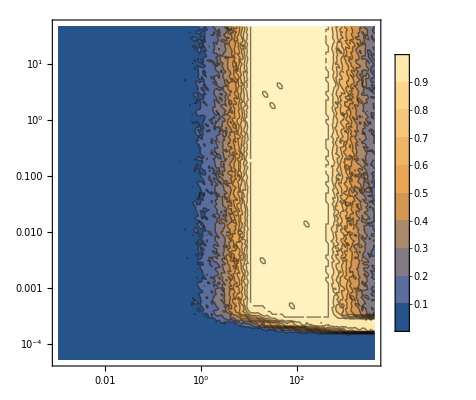

```mathematica
ListContourPlot[stats[[1;;,1;;3]],PlotLegends->Automatic,ScalingFunctions->{"Log10","Log10",Automatic}]
```

```mathematica
stopexec = DateObject[];
```

```mathematica
exectime = DateDifference[startexec,stopexec,"Second"]
```

20.7505 s